Лабораторная работа №6
Паде-Аппроксимация [n/n]

Диагональная Паде-аппроксимация в случае,  если    m=n    т.е. аппроксимация вида [n/n] 
func - изначальная функция
n- степень полинома
makePoly[n,x,a] - функция для формирование полинома степени n,   а - коэффициенты данного полинома

```mathematica
makePoly[n_Integer,x_Symbol,a_Symbol]:=Apply[Plus,(a[#]*x^#&/@Range[0,n])];
```

```mathematica
padeApprox[func_,xp_Symbol,n_Integer]:=Module[{chisl,x=xp,znamen,m=n, taylor, pade, system, k=2n, leftpart,var,solution, group,a,b},
chisl=makePoly[m,x,a];
znamen=(makePoly[m,x,b]/.b[0]:>1);
taylor=Normal@Series[func,{x,0,k}];
pade=chisl/znamen; 
chisl/znamen==taylor;
group=Collect[chisl-taylor*znamen,x];
leftpart=DeleteCases[CoefficientList[group,x],0]; 
system=(#==0)&/@leftpart;
var=DeleteCases[Flatten[CoefficientList[#,x]&/@{chisl,znamen}],_?NumericQ];
solution=Flatten[Solve[system[[;;Length@var]],var]]; 
pade=pade/.solution; 
pade

]
```

Пример 1

Рассмотрим функцию  f(x)=1/(1+Sin[x^2])

```mathematica
n={2,4,6};
```

```mathematica
padeApprox[1/(1+Sin[x^2]),x,#]&/@n
```

```mathematica
{1/(1+x^2),(1+x^4/6)/(1+x^2+x^4/6),(1+1 x^4/20)/(1+x^2+x^4/20-(7 x^6)/60)}
```

Сравним со встроенной функцией:

```mathematica
PadeApproximant[1/(1+Sin[x^2]),{x,0,#}]&/@n
```

{1/(1+x^2),(1+x^4/6)/(1+x^2+x^4/6),(1+x^4/20)/(1+x^2+x^4/20-(7 x^6)/60)}

Рассмотрим на графике полученный результат:

```mathematica
approx=padeApprox[1/(1+Sin[x^2]),x,#]&/@n;
```

n=2

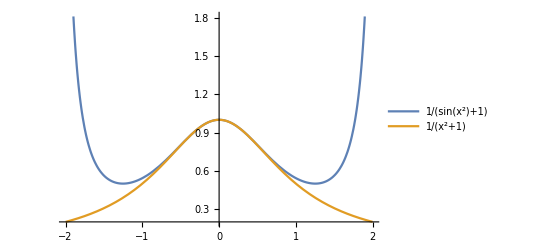

n=4

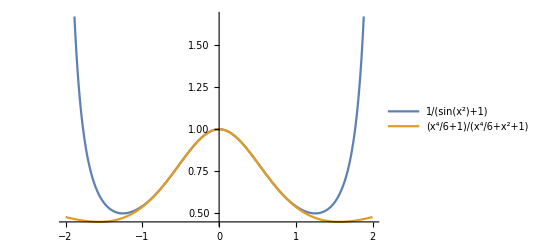

n=6

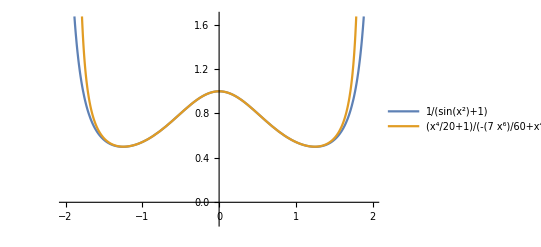

```mathematica
Do[Print["n=",n[[i]]];Print[Plot[{1/(1+Sin[x^2]),approx[[i]]},{x, -2, 2},PlotLegends->{1/(1+Sin[x^2]),approx[[i]]}]],{i,1,Length@n}]
```

Пример 2

Рассмотрим функцию  f(x)=ⅇ^(x+1)

```mathematica
n={2,3,4};
```

Рассмотрим на графике полученный результат:

```mathematica
approx=padeApprox[Exp[x+1],x,#]&/@n;
```

n=2

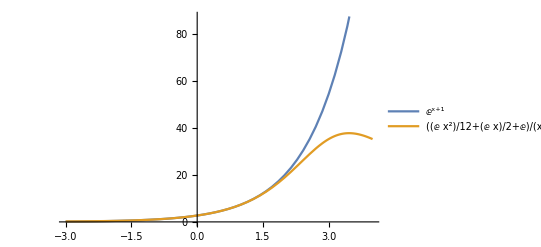

n=3

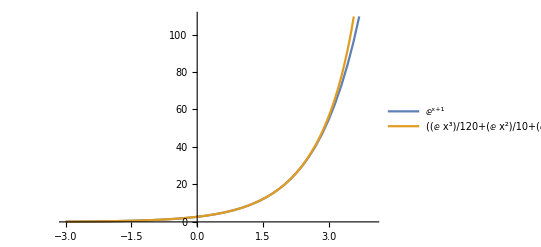

n=4

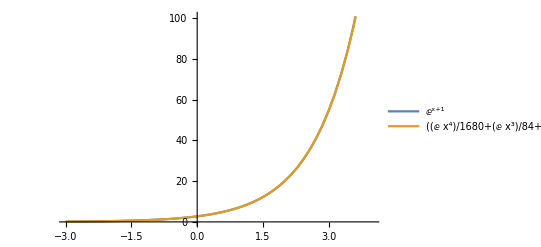

```mathematica
Do[Print["n=",n[[i]]];Print[Plot[{Exp[x+1],approx[[i]]},{x, -3,4},PlotLegends->{Exp[x+1],approx[[i]]}]],{i,1,Length@n}]
```